## Plot Examples-2 2D Plots of Functions

#### Plots of Predefined Functions

Sin[x] and Cos[x] are predefined functions. They can be readily plotted using prede
fined function Plot [ ],
Plot [function [free (independent) Variable] , {free (independent) Variable , initialValue , finalValue , options (if there is any)}]



```mathematica
p1=Plot[Sin[x],{x,0,2π}]
```

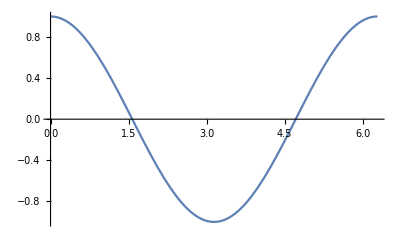

```mathematica
p2=Plot[Cos[x],{x,0,2π}]
```

We may combine them with more then one way,

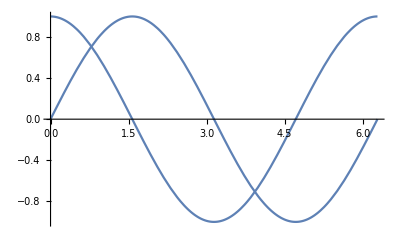

```mathematica
Show[p1,p2]
```

```mathematica
{p1, p2}
```

{-Graphics-,-Graphics-}

```mathematica
Row[{p1,p2}]
```

-Graphics--Graphics-

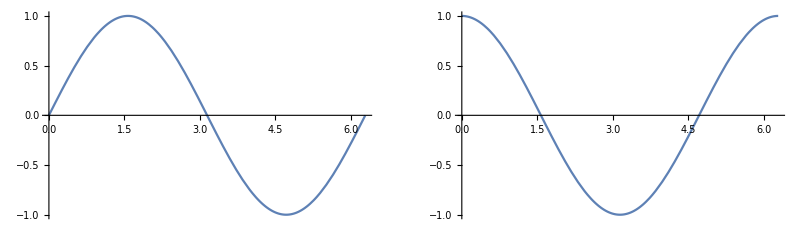

```mathematica
GraphicsRow[{p1,p2}]
```

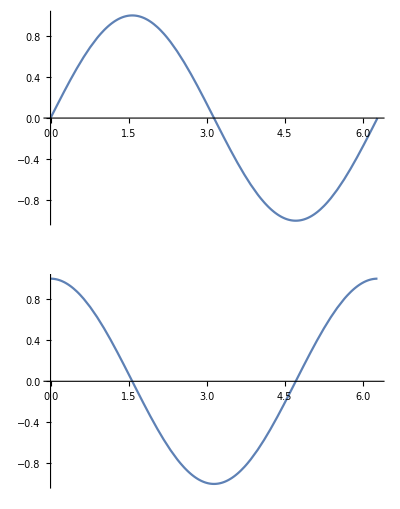

```mathematica
GraphicsGrid[{{p1},{p2}}]
```

#### Plots of User Defined Functions

```mathematica
f= x^2 2Exp[-x]Sin[x] ;
```

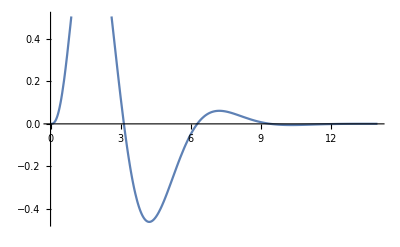

```mathematica
Plot[f,{x,0,14}]//TraditionalForm
```

```mathematica
Plot[f,{x,0,14}]//StandardForm
```

-Graphics-

```mathematica
Plot[f,{x,0,14}]// TexForm
```

TexForm[-Graphics-]

```mathematica
Plot[f,{x,0,14}]
```

-Graphics-

It is better, to define user defined functions as f[independentVariable_] : = Expression having one independentVariable declared in the definition of the function.

```mathematica
g[x_]:= 2 x^2 Exp[-x]Sin[x] ;
```

```mathematica
g[0]
```

0

```mathematica
g[20]//N
```

1.50538×10^-6

Functions are expressions which have single dependent variable (y) for any defined value of the independent variable (x). The interval which independent variable spans is called ``Domain” and related dependent variable interval ``Range”.

Every function give a single dependent variable (y) value, for any defined value of the independent variable (x). This constitutes an {x,y} point in 2D projection surface. That means functions produce a distinct point in a 2D area per defined values of the independent vaiable. We can explore these points using Table [ ] function of Mathematica.

```mathematica
t1 =Table[2 x^2 Exp[-x]Sin[x],{x, 0,20,0.02}]//N;
```

We can plot g[x] in the domain of x [0,20] with increments of 2, that will give the mapping of the points of t1 in 2D space. The procedure is explained in our paper .b4.b4ScatterPlot.pdf”.

```mathematica
t2 = Table[x,{x,0,20,0.02}];
```

```mathematica
t3 = {t2,t1}ᵀ;
```

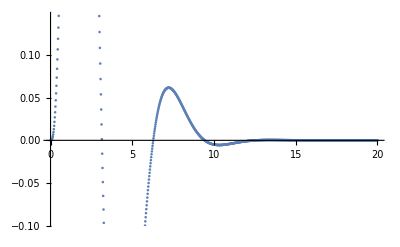

```mathematica
ListPlot[t3]
```

This not exact mapping of the t3 of course, Mathematica has produced more points for better explaining the peaks or downhills of the dataset t3. This is achieved with sophisticad curve fitting abilities of Mathematica.

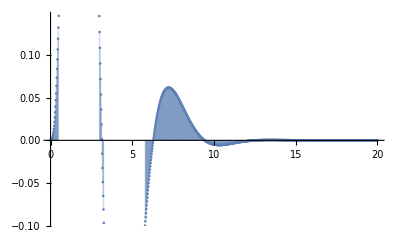

```mathematica
ListPlot[t3,Filling -> Axis]
```

Mathematica has issued normals to the x axis. This may be best understood by another less dense set.

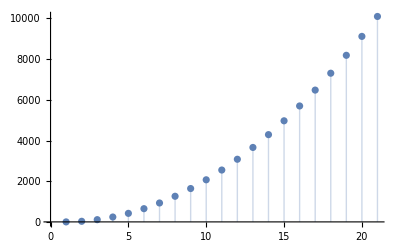

```mathematica
ListPlot[Table[x+ x^2, {x,0,100,5}],Filling -> Axis]
```

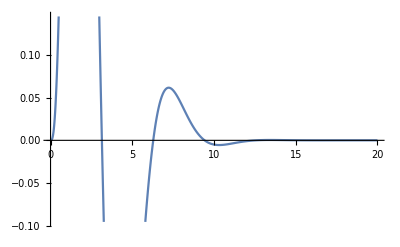

```mathematica
ListLinePlot[t3]
```

Mathematica has fitted a curve for joing the points of the list t3.

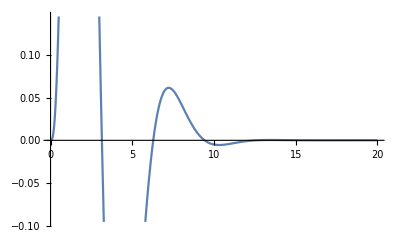

```mathematica
Plot[g[x],{x,0,20}]
```

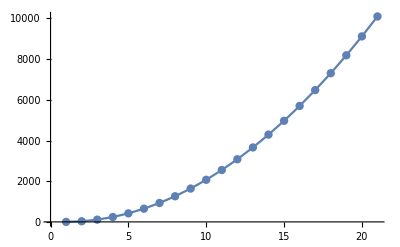

```mathematica
ListLinePlot[Table[x+ x^2, {x,0,100,5}],Mesh -> All]
```

This is another option applied to Plot [ ] function. Mathematica has produced a fitting lines like Bézier curves for joining the points of the vector supplied.

We can see all plots together :

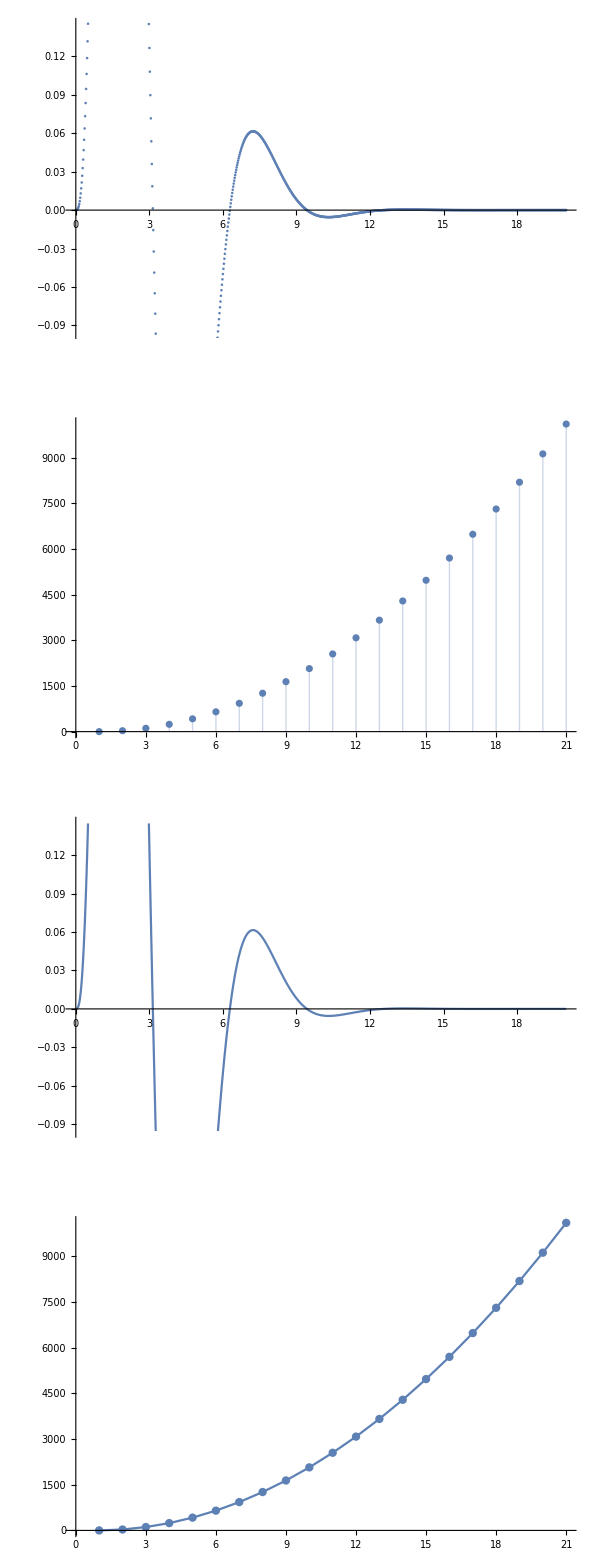

```mathematica
GraphicsGrid[
{
{ListPlot[t3]},
{ListPlot[Table[x+ x^2, {x,0,100,5}],Filling -> Axis]},
{ListLinePlot[t3]},
{ListLinePlot[Table[x+ x^2, {x,0,100,5}],Mesh -> All]}
},
ImageSize->600
]
```

ImageSize is another option for setting the size of the image produced by Mathematica. Alternatively it is possible to drag the edges of the image by mouse. Note that the GraphicsGrid [ ] function, produce a single image covering all the indicated plots.

The raw plot of the function y = 2 x^2 Exp[-x]Sin[x] at the domain [0,20], show discontinous regions in the up and down peak areas as . This is due to the range automatically chosen by Mathematica was too short to produce an adequate plot of the function in 2D space. We can add -for this case we must- to clarify by hand, what we have in mind for the range of this function when plotting with Mathematica. This is accomplished, by stating a range interval to the Plot [ ] function by means a ``PlotRange.b4.b4 option.

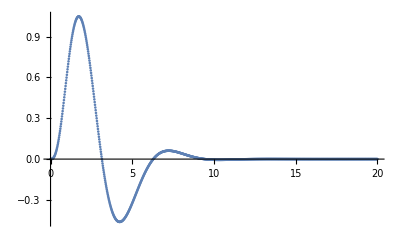

```mathematica
ListPlot[t3,PlotRange->Full]
```

We can also supply an user defined plot range :

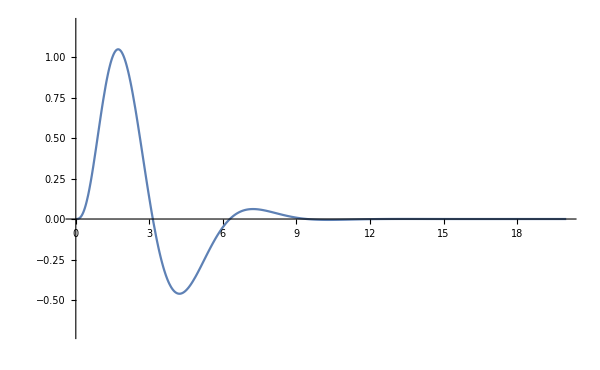

```mathematica
Plot[g[x],
{x,0,20},
PlotRange->{-0.7,1.2},
ImageSize->600
]
```

Fine. We are beginning to understand better the options for the Plot [ ] function of the Mathematica.

### Manipulations

Manipulations is changing some value affecting the function definition bzw. the plot of the function by mouse.

Manipulate[expression(u),{u,u_min,u_max}] (*  u any value between u_min,u_max *)

Manipulate[expression(u),{u,u_min,u_max,dt}] (*  u any value between u_min,u_max ,with steps of dt*)

```mathematica
Clear[a,b,d]; a =
```

```mathematica
Manipulate[Plot[Sin[a x] Cos[b x],
{x,0,2π },
PlotRange -> {-1.05,2.05},
ImageSize -> 400],
  {a,0,2},
  {b,0,2}
]
```

Drag a and b with mouse to some value other than 0 and you will see the plot with the new definitions for a and b.

```mathematica
Manipulate[
Plot[Sin[n x],{x,0,4π},
PlotRange->{-1.05,1.05},
ImageSize-> 400],
{n,1,5,1}]
```

Manipulations can only be active in Mathematica notebook files (*.nb). For publishing the notebooks contianing manipulations, one must publish them as (*.cdf) instead of [*.html or *.htm] or (*.pdf). The cdf reader is free and may be downloaded freely from Wolfram website. When published with other formats, manipulations may be observed but can not be manipulated.

### Options

Plots may be enhanced using various options. Mahematica offers a multitude options that can be implemented by the user. Bu the vaste number of these options make them very difficult to master all of these. The compromise is choosing from the options the ones that more generally applied to most instances of function plotting.

#### Frames

Plots in Mathematica are better shown by incorporating within a frame. Frames for plots are defined as :

For Graphicspaclet:ref/Graphics, Plotpaclet:ref/Plot, and related functions, Framepaclet:ref/Frame->{{left,right},{bottom,top}} specifies whether to draw a frame on each edge. With the default setting FrameTickspaclet:ref/FrameTicks->Automaticpaclet:ref/Automatic, ticks are included whenever a frame is drawn.

```mathematica
f1[x_]:=x Exp[x]; (* University of Texas in Austin *)
```

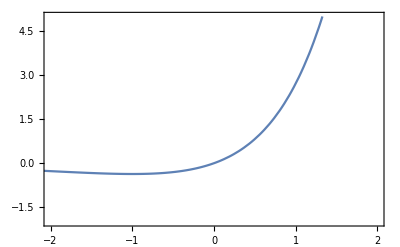

```mathematica
Plot[f1[x],
{x,-3,3},
PlotRange->{{-2,2},{-2,5}},
Frame->{{True,False}, {True,False}},
FrameTicks->{{True,False}, {True,False}},
Axes-> None 
]
```

Now frames become equivalents of axes. The motivation of axes/Frame interchange is the oppotunity to label the frame at the middle of the frame. This opportunity is not given to the axes specification which may only labeled at their extreme ends by their predefined function. But this is possible with using Text [ ] subroutine of the Graphics [ ] function. This will be shown at the later pages of this manuscript.

There are many options for making the labels more stylish or prone to publication.

Each label may have only one option without applying Directive rule.

```mathematica
Plot[f1[x],
{x,-3,3},
PlotRange->{{-2,2},{-2,5}},
(*Frame->True, for framing the whole image *)
Frame->{{True,False}, {True,False}},
FrameTicks->{{True,False}, {True,False}},
FrameTicksStyle->Directive[Thick,Italic],
Axes-> None 
]
```

-Graphics-

```mathematica
Plot[f1[x],
{x,-3,3},
PlotRange->{{-2,2},{-2,5}},
Frame->{{True,False}, {True,False}},
FrameTicks->{{True,False}, {True,False}},
FrameTicksStyle->{{Red,None},{Blue,None}},
Axes-> None
 
]
```

-Graphics-

The styles of the frames drawn in above plot are colored by means of FrameTicksStyle rule. It can handle only one option without calling Directive [ ] function. Mathematica has multitude of ways of specify colors. We may consult Mathematica Documents for how to specify colors and try them using this plotting template.

```mathematica
Plot[f1[x],
{x,-3,3},
PlotRange->{{-2,2},{-2,5}},
Axes-> None,
Frame->{{True,False}, {True,False}},
FrameTicks->{{True,False}, {True,False}},
FrameTicksStyle->{{{Darker[Green],Thick},None},{{Darker[Orange],Thick},None}}
 
]
```

-Graphics-

With Directive [ ] function we have more opportunities,

```mathematica
Plot[f1[x],
{x,-3,3},
PlotRange->{{-2,2},{-2,5}},
Axes-> None,
Frame->{{True,False}, {True,False}},
FrameTicks->{{True,False}, {True,False}},
FrameTicksStyle->{{{Directive[Darker[Green],Thick]},None},{{Directive[Darker[Orange],Thick]},None}}
 
]
```

-Graphics-

With Directive Function, we can also set FontFamily and FontSize rules together with a colored text.

```mathematica
Plot[f1[x],
{x,-3,3},
PlotRange->{{-2,2},{-2,5}},
Axes-> None,
Frame->{{True,False}, {True,False}},
FrameTicks->{{True,False}, {True,False}},
FrameTicksStyle->{{{Directive[Darker[Green],FontFamily->"SegoeUI", FontSize->16],Thick},None},{{Directive[Darker[Orange],FontFamily->"SegoeUI", FontSize->16],Thick},None}}
 
]
```

-Graphics-

Labeling of the Plot is made by applying PlotLabel rule with LabelStyle [ ] function. The Directive [ ] function may be called for more styling options.

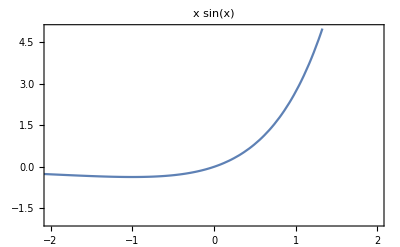

```mathematica
Plot[f1[x],
{x,-3,3},
PlotLabel->"x sin(x)",
LabelStyle->Directive[Red,FontFamily->"SegoeUI", FontSize->16],
PlotRange->{{-2,2},{-2,5}},
Axes-> None,
Frame->{{True,False}, {True,False}},
FrameTicks->{{True,False}, {True,False}},
FrameTicksStyle->{
{{Directive[Darker[Green],FontFamily->"SegoeUI", FontSize->16],Thick},None},{{Directive[Darker[Orange],FontFamily->"SegoeUI", FontSize->16],Thick},None}
}
 ]
```

FrameLabel → rule may be applied for labeling the edges of the frame with style.

FrameLabelpaclet:ref/FrameLabel→Nonepaclet:ref/None specifies that no labels should be given.

FrameLabelpaclet:ref/FrameLabel→label specifies a label for the bottom edge of the frame.

FrameLabelpaclet:ref/FrameLabel→{bottom,left} specifies labels for the bottom and left-hand edges of the frame.

FrameLabelpaclet:ref/FrameLabel→{{left,right},{bottom,top}} specifies labels for each of the edges of the frame.

Any expression can be specified as a label. It will be given by default in TraditionalFormpaclet:ref/TraditionalForm. Arbitrary strings of text can be given as "text". »

Labels for the vertical edges of the frame are written vertically by default . For the horizontal labels we may set RotateLabelpaclet:ref/RotateLabel→Falsepaclet:ref/False.

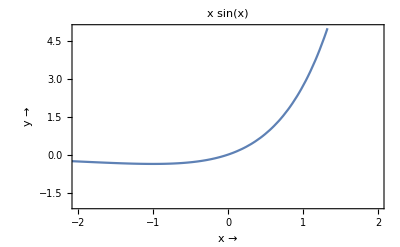

```mathematica
Plot[f1[x],
{x,-3,3},
PlotRange->{{-2,2},{-2,5}},
PlotRegion->All,
PlotLabel->"x sin(x)",
LabelStyle->Directive[Red,FontFamily->"SegoeUI", FontSize->16],
Axes-> None,
Frame->{{True,False}, {True,False}},
FrameTicks->{{True,False}, {True,False}},
FrameTicksStyle->{
{{Directive[Darker[Green],FontFamily->"SegoeUI", FontSize->16],Thick},None},{{Directive[Darker[Orange],FontFamily->"SegoeUI", FontSize->16],Thick},None}
},
FrameLabel->{
{Style["y →",Darker[Green], FontFamily-> "Segoe UI", FontSize->16],None},{Style["x →",Darker[Orange], FontFamily-> "Segoe UI", FontSize->18],None}
}
 
]
```

The following settings can be given for GridLinespaclet:ref/GridLines:

With the Automaticpaclet:ref/Automatic setting, grid lines are usually placed at points whose coordinates have the minimum number of digits in their decimal representation.

For each direction, the following grid line options can be given:

Nonepaclet:ref/None | no grid lines drawn

Automaticpaclet:ref/Automatic | grid lines placed automatically

{xgrid , y grid}  grid lines specified separately in each direction,

func     a function to be applied to x_min, x_max to get the grid line option

```mathematica
{{{Subscript[x, 1],Subscript[x, 2],…}, grid lines drawn at the specified positions}}
```

{{{x_1,x_2,…},grid lines drawn at the specified positions }}

```mathematica
{{{{Subscript[x, 1],Subscript[style, 1]},…}, grid lines with specified styles}}
```

{{{{x_1,style_1},…},grid lines with specified styles }}

Grid line styles can involve any graphics directives, such as RGBColorpaclet:ref/RGBColor and Thicknesspaclet:ref/Thickness.

The grid line function func[x_min,x_max] may return any other grid line option.

AbsoluteOptionspaclet:ref/AbsoluteOptions gives the explicit form of GridLinespaclet:ref/GridLines specifications when Automaticpaclet:ref/Automatic settings are used.

GridLinesStylepaclet:ref/GridLinesStyle gives default styles to use for grid lines.

GridLinesStylepaclet:ref/GridLinesStyle->style specifies that all grid lines should be rendered by default with the specified style.

GridLinesStylepaclet:ref/GridLinesStyle->{xstyle,ystyle} specifies that x and y grid lines should use different styles.

Styles can be specified using graphics directives such as Thickpaclet:ref/Thick, Redpaclet:ref/Red, and Dashedpaclet:ref/Dashed, as well as Thicknesspaclet:ref/Thickness, RGBColorpaclet:ref/RGBColor, Dashingpaclet:ref/Dashing, and combinations given by Directivepaclet:ref/Directive.

Style specifications can refer to styles using style names from current stylesheets.

Any outside styles not explicitly overridden by settings in GridLinesStylepaclet:ref/GridLinesStyle will still be used.

Explicit styles specified in the settings for GridLinespaclet:ref/GridLines can override styles specified in GridLinesStylepaclet:ref/GridLinesStyle.

The default style of axes is specified by the option DefaultGridLinesStylepaclet:ref/DefaultGridLinesStyle.

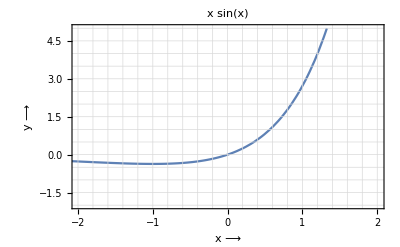

```mathematica
Plot[f1[x],
{x,-3,3},
PlotRange->{{-2,2.01},{-2,5}},
PlotRegion->All,
PlotLabel->"x sin(x)",
LabelStyle->Directive[Red,FontFamily->"SegoeUI", FontSize->16],
Axes-> None,
Frame->{{True,False}, {True,False}},
FrameTicks->{{True,False}, {True,False}},
FrameTicksStyle->{{{Directive[Darker[Green],FontFamily->"SegoeUI", FontSize->16],Thick},None},{{Directive[Darker[Orange],FontFamily->"SegoeUI", FontSize->16],Thick},None}},
FrameLabel->{{Style["y ⟶",Darker[Green], FontFamily-> "Segoe UI", FontSize->16],None},{Style["x ⟶",Darker[Orange], FontFamily-> "Segoe UI", FontSize->16],None}},
GridLines->{ {-2,-1.8,-1.6,-1.4,-1.2,-1,-0.8,-0.6,-0.4,-0.2,{0,Thick},0.2,0.4,0.6,0.8,1,1.2,1.4,1.6,1.8,2},{-2,-1.5,-1,-0.5,{0,Thick},0.5,1,1.5,2,2.5,3,3.5,4,4.5,5}},
GridLinesStyle->{{Darker[Orange]},{Darker[Green]}}
 
]
```

For a last touch , we’ll adjust the size of the image,

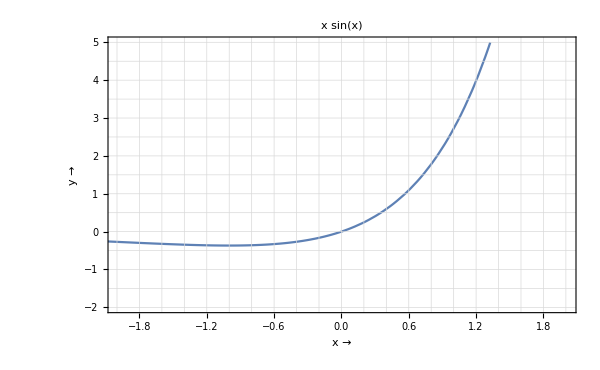

```mathematica
Plot[f1[x],
{x,-3,3},
PlotRange->{{-2,2.01},{-2,5}},
PlotRegion->All,
PlotLabel->"x sin(x)",
LabelStyle->Directive[Red,FontFamily->"SegoeUI", FontSize->16],
Axes-> None,
Frame->{{True,False}, {True,False}},
FrameTicks->{{True,False}, {True,False}},
FrameTicksStyle->{{Directive[Darker[Green],FontFamily->"SegoeUI", FontSize->16,Thick],None},{Directive[Darker[Orange],FontFamily->"SegoeUI", FontSize->16],None}},
FrameLabel->{{Style["y →",Darker[Green], FontFamily-> "Segoe UI", FontSize->16],None},{Style["x →",Darker[Orange], FontFamily-> "Segoe UI", FontSize->16,Thick],None}},
GridLines->{ {-2,-1.8,-1.6,-1.4,-1.2,-1,-0.8,-0.6,-0.4,-0.2,{0,Directive[Thick,Dashing[{}]]},0.2,0.4,0.6,0.8,1,1.2,1.4,1.6,1.8,2},{-2,-1.5,-1,-0.5,{0,Directive[Thick,Dashing[{}]]},0.5,1,1.5,2,2.5,3,3.5,4,4.5,5}},
GridLinesStyle->{{Darker[Orange],Thick,Dashed},{Darker[Green],Thick,Dashed}},
ImageSize->600
]
```

We can easily watch narrower domains in order to understand better the behavior of the function. Example :

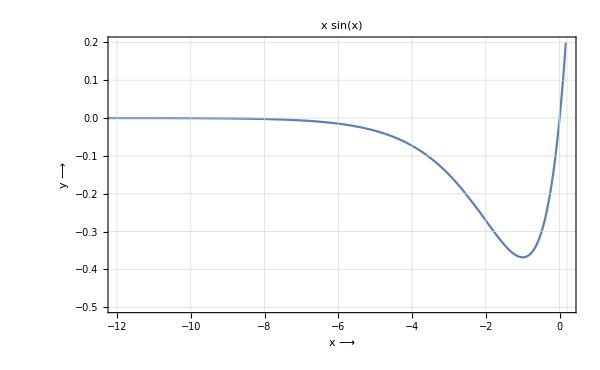

```mathematica
Plot[f1[x],
{x,-20,3},
PlotRange->{{-12,0.2},{-0.5,0.2}},
PlotRegion->All,
PlotLabel->"x sin(x)",
LabelStyle->Directive[Red,FontFamily->"SegoeUI", FontSize->16],
Axes-> None,
Frame->{{True,False}, {True,False}},
FrameTicks->{{True,False}, {True,False}},
FrameTicksStyle->{{Directive[Darker[Green],FontFamily->"SegoeUI", FontSize->16],None},{Directive[Darker[Orange],FontFamily->"SegoeUI", FontSize->16],None}},
FrameLabel->{{Style["y ⟶",Darker[Green], FontFamily-> "Segoe UI", FontSize->16,Thick],None},{Style["x ⟶",Darker[Orange], FontFamily-> "Segoe UI", FontSize->16,Thick],None}},
GridLines->{ {-12,-10.0,-8,-6,-4,-2,{0,Directive[Thick]},0.2},{-0.5,-0.4,0.3,-0.3,-0.2,-0.1,{0,Directive[Thick]},0.1,0.2}},
GridLinesStyle->{{Thick,Darker[Orange]},{Thick,Darker[Green]}},
ImageSize->600
]
```

Obtaing black and white versions are more easy.

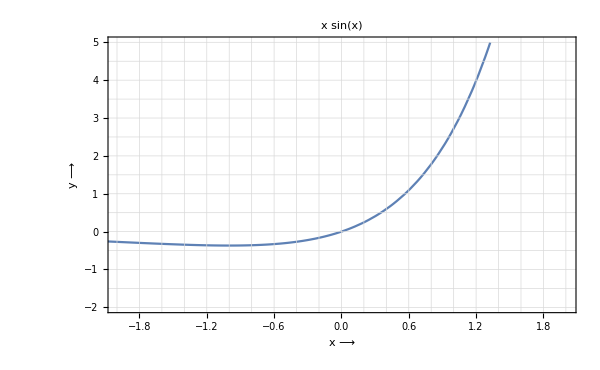

```mathematica
Plot[f1[x],
{x,-3,3},
PlotRange->{{-2,2.01},{-2,5}},
PlotRegion->All,
PlotLabel->"x sin(x)",
LabelStyle->Directive[FontFamily->"SegoeUI", FontSize->16,Black],
Axes-> None,
Frame->{{True,False}, {True,False}},
FrameTicks->{{True,False}, {True,False}},
FrameTicksStyle->{
{Directive[Darker[Black],FontFamily->"SegoeUI", FontSize->16],None},{Directive[Darker[Black],FontFamily->"SegoeUI", FontSize->16],None}
},
FrameLabel->{
{Style["y ⟶",Darker[Black],FontFamily-> "Segoe UI", FontSize->16],None},{Style["x ⟶",Darker[Black],FontFamily-> "Segoe UI", FontSize->16],None}
},
GridLines->{ 
{-2,-1.8,-1.6,-1.4,-1.2,-1,-0.8,-0.6,-0.4,-0.2,{0,Directive[Thick]},0.2,0.4,0.6,0.8,1,1.2,1.4,1.6,1.8,2},{-2,-1.5,-1,-0.5,{0,Directive[Thick]},0.5,1,1.5,2,2.5,3,3.5,4,4.5,5}
},
GridLinesStyle->{Lighter[Black],Lighter[Black]},
ImageSize->600
]
```

### Aspect Ratio

Aspect ratio is the ratio y/x and may be set by the user or set as Automatic or unstated by leaving the arrangement to its default value

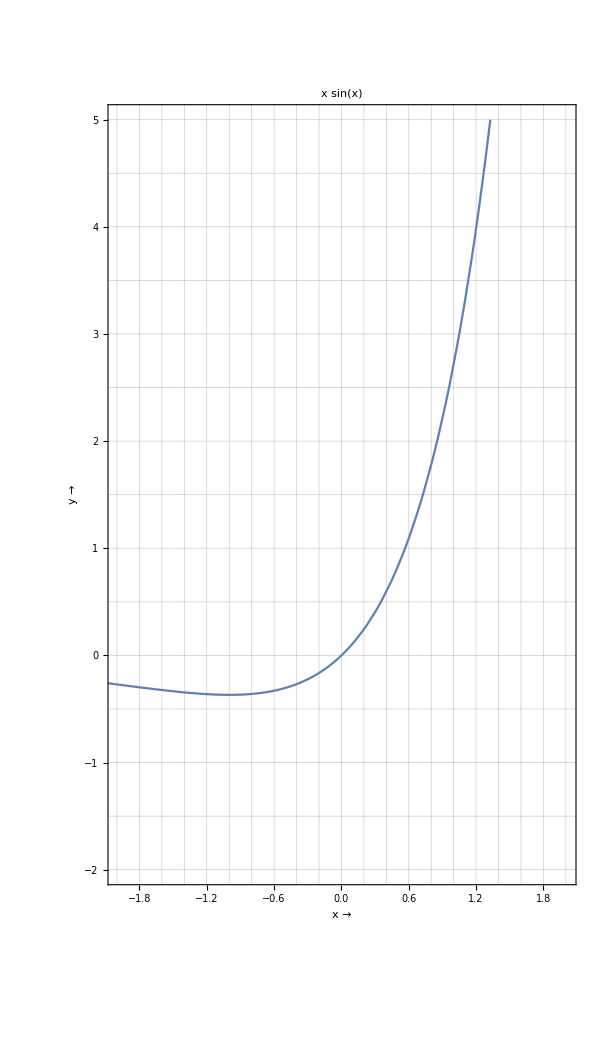

```mathematica
Plot[f1[x],
{x,-3,3},
PlotRange->{{-2,2.01},{-2,5}},
PlotRegion->All,
AspectRatio->Automatic,
PlotLabel->"x sin(x)",
LabelStyle->Directive[FontFamily->"SegoeUI", FontSize->16],
Axes-> None,
Frame->{{True,False}, {True,False}},
FrameTicks->{{True,False}, {True,False}},
FrameTicksStyle->{{Directive[FontFamily->"SegoeUI", FontSize->16],None},{Directive[FontFamily->"SegoeUI", FontSize->16],None}},
FrameLabel->{{Style["y →",FontFamily-> "Segoe UI", FontSize->16],None},{Style["x →",FontFamily-> "Segoe UI", FontSize->16],None}},
GridLines->{ {-2,-1.8,-1.6,-1.4,-1.2,-1,-0.8,-0.6,-0.4,-0.2,{0,Directive[Thick]},0.2,0.4,0.6,0.8,1,1.2,1.4,1.6,1.8,2},{-2,-1.5,-1,-0.5,{0,Directive[Thick]},0.5,1,1.5,2,2.5,3,3.5,4,4.5,5}},
ImageSize->600
]
```

The deafult is 1/GoldenRatio and if it is the case, we do not have to mention it in the graph program.

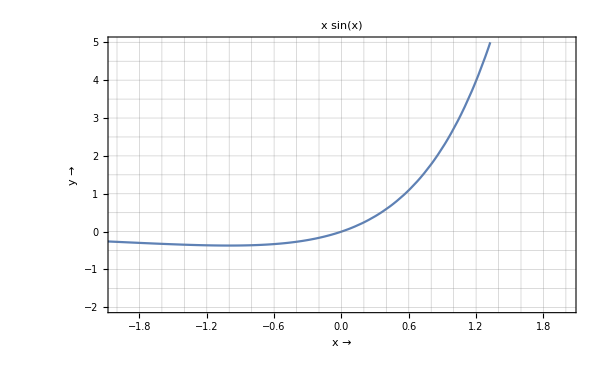

```mathematica
Plot[f1[x],
{x,-3,3},
PlotRange->{{-2,2.01},{-2,5}},
PlotRegion->All,
AspectRatio->1/GoldenRatio,
PlotLabel->"x sin(x)",
LabelStyle->Directive[FontFamily->"SegoeUI", FontSize->16],
Axes-> None,
Frame->{{True,False}, {True,False}},
FrameTicks->{{True,False}, {True,False}},
FrameTicksStyle->{
{Directive[FontFamily->"SegoeUI", FontSize->16],None},{Directive[FontFamily->"SegoeUI", FontSize->16],None}
},
FrameLabel->{
{Style["y →",FontFamily-> "Segoe UI", FontSize->16],None},{Style["x →",FontFamily-> "Segoe UI", FontSize->16],None}
},
GridLines->{ 
{-2,-1.8,-1.6,-1.4,-1.2,-1,-0.8,-0.6,-0.4,-0.2,{0,Directive[Thick]},0.2,0.4,0.6,0.8,1,1.2,1.4,1.6,1.8,2},{-2,-1.5,-1,-0.5,{0,Directive[Thick]},0.5,1,1.5,2,2.5,3,3.5,4,4.5,5}
},
ImageSize->600
]
```

Every function, except the Identity function y = x, result with different values of range for a fixed domain. Therefore the setting of aspect ratio is of ultime importance. We should consider carefully the trend of our function and choose a proper aspect ratio. By the way, for the Identity function,

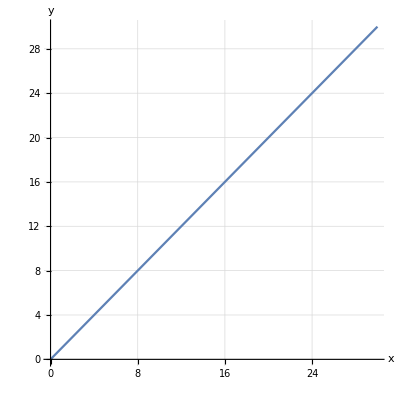

```mathematica
Plot[y=x,{x, 0,30},
AspectRatio->1,
GridLines->Automatic, 
AxesLabel->
{
Style["x",FontFamily-> "Segoe UI", FontSize->16],
Style["y",FontFamily-> "Segoe UI", FontSize->16]
}
]
```

We can try different aspect ratios for specific functions and find the best one that fit our needs.

### Discontinuous Functions

Not All fonctions are continuous in the domain (-∞,∞) that is, some values of the dependent variable of this domain do not produce known values of the function. This is called ``discontinuation”. Discontinuation property is purely dependent of the configuration of the function. Functions which exhibit discontinuties are called ``Discontinious Functions” .

Most rational functions exhibit discontinuative property owing to certain values of x which produce a/0 ratio, with a being a real number.

Function discontinuity is not a simple subject to tackle at once. We should get proper familiarity about the discontinuties of the functions. A website defining concisely and comprehensibly the subject is https://www.math24.net/discontinuous-functions/ . We will follow the subject from their web pages. First discontinuity map devised according the definitions of this site is  presented blow:

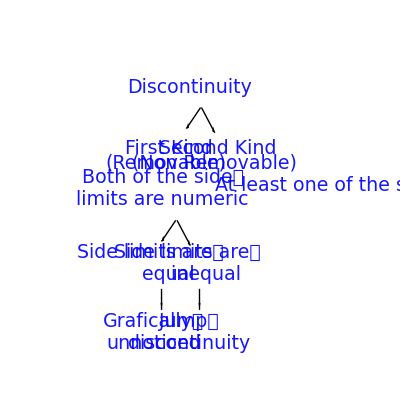

If f(x) is not continuous at x=a, then f(x) is said to be discontinuous at this point. Figures 1−4 show the graphs of four functions, two of which are continuous at x=a and two are not.

-Graphics-

-Graphics-

#### Classification of Discontinuity Points

-Graphics-

We will begin with discontinuities of first kind. The functions having defined limits in both sides of the point x = a , (a) being a real number in the domain of the function and the limits of the function are real and equal to each other in both sides of (a) is a function having first class removable discontiniuty which is not a jump discontinuation property. we will call these functions as ``Functions having ``A” type first class discontinuation property. Functions which exhibit jump discontinuity will be called as ``B” type first class discontinuation.

For understanding whether the function has some kind of discontinuation we will look at first to its graph. But careful : First class A type discontinuations (without a jump) can not be spotted from their graphs. Graphs may only reveal first class jump discontinuations (class B) and second kind non removable discontinuations. Then mathematical investigation in form of finding both side limits must be taken into account. We will follow these paths in examining the functions about their discontinuities.

Since we will need to find some limits and roots of equations, it is important to know, how the limits and roots of equations are found with Mathematica.

#### Limits in Mathematica

Limits in Mathematica are found by the application of the function Limit [ ]. The general form of application for any function f[x] defined previously .

Limit[f[x] , x → a]

For finding the lower (left) or upper (right) limit when x aproaching a,

Limit[f[x] , x → a-0] and Limit[f[x] , x → a+0]

or,

Limit[f[x] , x → a ,Direction→ -1] and Limit[f[x] , x → a Direction→1]

Limit[f[x] , x → a ,Direction→ -1]  means the limit of the function f[x] when x tends to a, approaching from above. (-1 means from +∞ to -∞) or (from right to left)

Limit[f[x] , x → a ,Direction→ 1]  means the limit of the function f[x] when x tends to a, approaching from below. (1 means from -∞ to 4∞) or (from left to right).

#### Roots of the equations with Mathematica

Mathematica include different  methods for finding the roots of equations. Normally using Solve [ ] function wiil be enough to spotting the roots of most equations. but for problematic ones, one may try more sophisticated functions provided form mathematica.

Usage of Solve function is,

Solve[f[x](== for equal, < for less than, > for greater than) right side term, {independentVariable}]

We are now ready for looking after the discontinuities.

```mathematica
Examples
```

Examples

Find a discontiniuty of the function,

f[x_]:= (2 x^4-12 x)/((3-x^6)(1+x^4))

Solution :

Altough it not fully informative about all the discontinuities (discontinuities of the first class type A can not be understood from the graph of the function) we will always begin by investigation of the graph of a function. Bu we will not rely completely on the primary information obtained form the graph for the final decision about the discontinuity of the function examined.

```mathematica
Clear[f,x,n]
```

```mathematica
f[x_]:= (2 x^4-12 x)/((3-x^6)(1+x^4))
```

```mathematica
FullSimplify[f[x]]
```

-(2 x (-6+x^3))/((1+x^4) (-3+x^6))

The graph of this function,

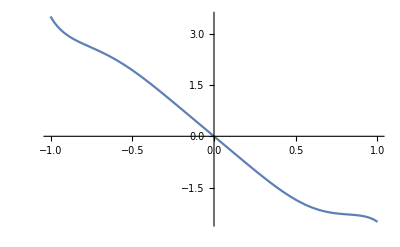

```mathematica
Plot[f[x],{x, -1,1}]
```

The graph show a false impression so that an unaware may decide that the given function is continous. In fact it is not. Since the given function has not changed its structure and still rational after the simplification, we will examine whether the function becomes a/0 form after some values of the independent variable.

For clarifying this situation, we will make an equation with the denominator term of the given function equals to zero. For our example,

```mathematica
Solve[(1+x^4) (-3+x^6) ==0, {x}]
```

{{x→-(-1)^(1/4)},{x→(-1)^(1/4)},{x→-(-1)^(3/4)},{x→(-1)^(3/4)},{x→-3^(1/6)},{x→3^(1/6)},{x→-(-1)^(1/3) 3^(1/6)},{x→(-1)^(1/3) 3^(1/6)},{x→-(-1)^(2/3) 3^(1/6)},{x→(-1)^(2/3) 3^(1/6)}}

We got number of roots, some of them are real, some of them is complex. But for tems of discontinuity real or complex values makes no difference they all cause discontinuities.

Plots of functions having discontinuities with Mathematica, result with graphs where the asymptotes are not shown. To make them visible, we have to add some options.

Plot[f, {x, a,b}, Exclusions → {list}]

Mathematica, by default take  Exclusions → All, to make them visible we should turn it to  Exclusions → None

```mathematica
Plot[f[x],{x, -1, 1},Exclusions->None]
```

-Graphics-

Plots of Mathematica can not indicate the points where the function has type A discontinuity. We should not rely to the Mathematica plots on the subject, the final decision must be taken only after mathematical analysis.

#### Example

Find a discontiniuty of the function,

```mathematica
Clear[f,x]
```

```mathematica
f[x_]:= 1/(x-1)
```

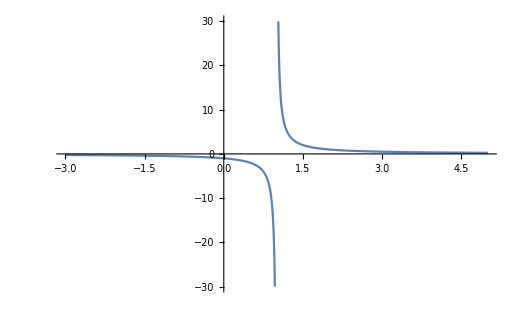

```mathematica
Plot[f[x],{x,-3,5},
PlotRange->{-30,30},
PlotRegion->All
]
```

The neighborhood of a region where small changes of the independent variable result big changes of the dependent variable is the region of discontinuity of the function. From the graphical result, we conclude that the given function has a type 2 unremovable discontinuity at x = 1 . The plot also show that an asymptotic line exist at x = 0 . We will bring the vertical asymptote at light by adding the option, Exclusion → None.

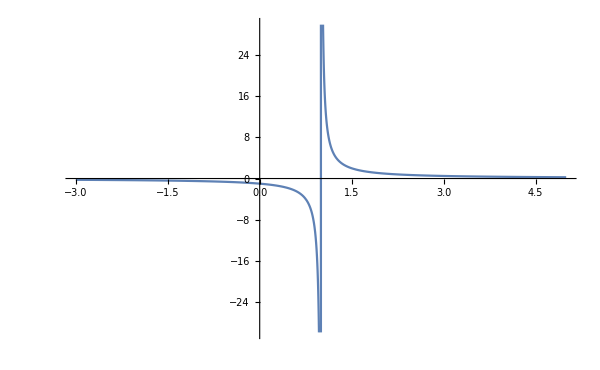

```mathematica
Plot[f[x],{x,-3,5},
PlotRange->{-30,30},
PlotRegion->All,
Exclusions->None,
ImageSize->600
]
```

Clearly, the function 1/(x-1) has a vertical asymptote, normal to the x axis at point {1 , 0} indicated by the graph of the function. But we must always find the exact values by mathematical methods.

```mathematica
Solve[x-1==0,{x}]
```

{{x→1}}

Mathematica confirms that the given function has an asimptote at x = 1 as,

```mathematica
f[1]
```

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

Whether the upper and lower limits from each side exists, will be detected by Mathematica,

```mathematica
Limit[f[x], x->1+0] (* Left Limit *)
```

Indeterminate

```mathematica
Limit[f[x], x-> 1-0] (* Right Limit *)
```

Indeterminate

The limit examination with Mthematica, reveals that, limits in both directions in the discontinuity point x = 1, is Indeterminate in both sides.This indicates that the given function has an essential (unremovable) discontinuity named ``Discontinuity of the Second Kind” at the point x = 1.

#### Example

Find whether the function y = 3^(x/(1-x^2)) has discontinuities.

Solution

We’ll begin by tracing its graph.

```mathematica
Clear[f,x]
```

```mathematica
f[x_]:=3^(x/(1-x^2))
```

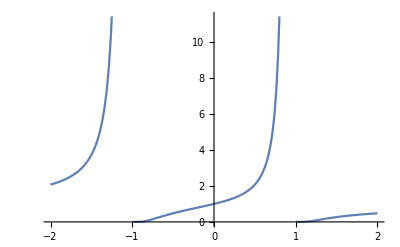

```mathematica
Plot[f[x],{x,-2,2}]
```

The function indicates that the given function has two discontinuities about 1 and -1, let us spot them more precisely.

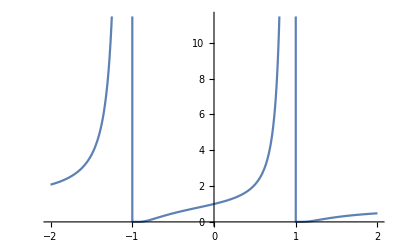

```mathematica
Plot[f[x],{x,-2,2},Exclusions->None]
```

The graphic output show that there is two asymptotes at -1 and 1 . More precise locations will be indicated by more detailed graphs.

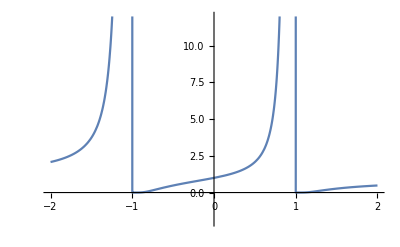

```mathematica
Plot[f[x],{x,-2,2},PlotRange->{-2,12},Exclusions->None]
```

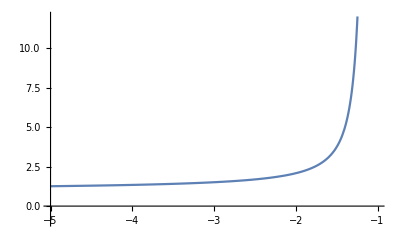

```mathematica
Plot[f[x],{x,-5,-1},PlotRange->{-1, 12},Exclusions->None]
```

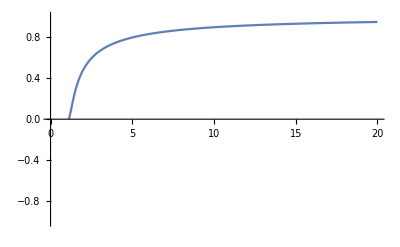

```mathematica
Plot[f[x],{x,1+0.1,20},PlotRange->{-1,1},Exclusions->None]
```

```mathematica
Plot[f[x],{x,-2,0},PlotRange->All,Exclusions->None]
```

-Graphics-

```mathematica
Plot[f[x],{x,0,2},PlotRange->All,Exclusions->None]
```

-Graphics-

It is confirmed that the given function has two discontinuities at the points x = -1 and x =1 . Let us look with a bigger image sizes,

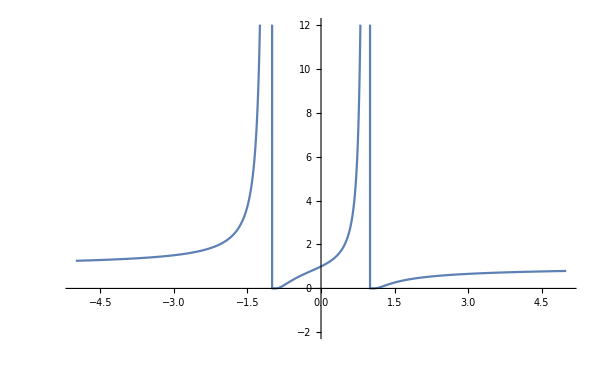

```mathematica
Plot[f[x],{x,-5,5},PlotRange->{-2,12},Exclusions->None,ImageSize->600]
```

More precise locations of aymptotic lines, are to be found by mathematical analysis.

The function structure is of type n^a and indeterminable when n^indeterminate. We will look for an x which will cause, x/(1-x^2) indeterminate. Let  us simplify this rational expression.

(x/x)/((1-x^2)/x) = 1/((1-x^2)/x)= 1/(1/x-x)

1/x-x =0; 1/x = x ;  x^2 = 1 ; √(x^2) = 1 ;x=1 or x=-1

or,

(1/x)/x= 0 ; 1/x^2 = 0 ; x^2 = 1 ; x^2 - 1 = 0 ; (x-1)(x+1) = 0; x = 1 or x = -1

or simply

```mathematica
Solve[1/x-x == 0, x]
```

{{x→-1},{x→1}}

These two values make 1/x-x equal to zero, this  makes  1/(1/x-x) indeterminate which makes in turn, 3^indeterminate as indeterminate. The points (-1) and (1)  are the discontinuity points found algebraically and they are confirmed by the graph of this function.

Upper and lower limits  in the neighborhood of these points, will show the type of discontinuity of this function.

```mathematica
{Limit[f[x],x->-1-0],Limit[f[x],x->-1+0]}
```

{Indeterminate,Indeterminate}

```mathematica
{Limit[f[x],x->1-0],Limit[f[x],x->1+0]}
```

{Indeterminate,Indeterminate}

For the final result, the given function is determined to have essential, nonremovable second class discontinuities at the points x = -1 and x =1. This is supporting by mathematical anaysis and by the results obtained from graphical investigations.

#### Example

Find the discontinuities of the function y = Sin[x]/x.

Solution

```mathematica
Clear[f,x]
```

```mathematica
f[x_]:= Sin[x]/x
```

First we plot this function as usual :

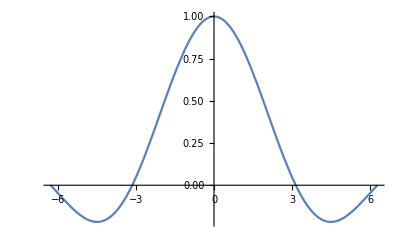

```mathematica
Plot[f[x], {x, -2π,2π}]
```

At first sight, the function seems to be continious by its graph. But, this is not the case. We should not forget there is a single x in the denominator. When this x will be equal to zero in the range [-2 , 2] the function will have a discotinuity.

From the plot of this function, we observe that the discontinuity is not a jump discontinuty, in contrary it is a point  discontinuty. This will imply also that if x will be near in both sides about ϵ (epsilon) the function will tend to its limit δ =1 in both side the value of the discontinuity without being equal to it. Then various types of discontiuties occur depending the structure of the function.This is first class A type removable discontinuity because the limits of both sides of the asymptotic line is real and equal to each other. This make this function piecewise, but contigious in -ϵ and + ϵ advances of the independent variable (x) before and after the point of discontinuity.

This make the function piecewise but this stay unnoticed when inspecting the graph of the function. To understand the piecewise behavior of the function we will graph each piece separately :

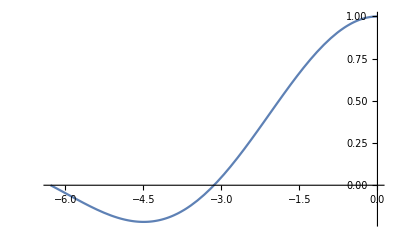

```mathematica
Plot[f[x], {x, -2π,0}]
```

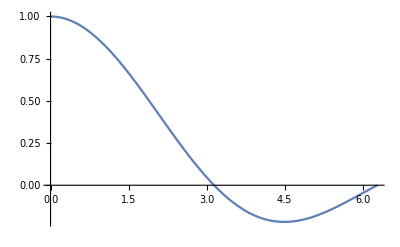

```mathematica
Plot[f[x], {x, 0,2 π}]
```

The plot of this function is nothing than a seamless plotting of both pieces separately but contigiously due to the sophisticated intricate plotting function of Mathematica, which plot the first order class A functions aa a single graph whose discontinuities can not be noticed by eyes. Even adding the option ``Exclusions→None” will not help for having the exlusion point be inserted within the graph.

Mathematica has a Piecewise[ ] function but this function is most useful in function having jump discontinuities and essential discontinuities . For function plotting,  simple Plot [ ] function will suffice, with or without ``Exclusions→None” option. Note that for the functions having first order class A discontinuities stating Exclusions→ All is unnecessary.

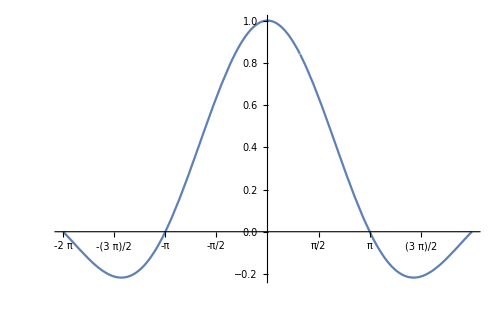

```mathematica
Plot[Piecewise[{{f[x],x<1},{f[x], x>1}}],{x, -2π,2π},Exclusions->{1},
Ticks-> {{-2π,-3/2  π,-π, -1/2  π,  1/2π,π,3/2π},Automatic},ImageSize->500
]
```

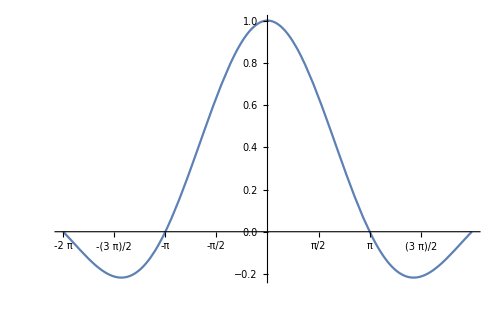

```mathematica
Plot[f[x],{x, -2π,2π},
Ticks-> {{-2π,-3/2  π,-π, -1/2  π,  1/2π,π,3/2π},Automatic},ImageSize->500
]
```

Adding Piecewise[ ] function is not enhancing the graph compared to the graph produced by a simple Plot [ ] function.

This function has a removable discontinuity at at x=0. This cannot be seen in graphs and even Mathematica does not help. The discontinuity may only be understood by finding the value of the independent variable (x) which makes the value of the function ``Unknown” and this value is conventionally considered as ``Infinity” (∞) .

The function  Sin[x]/x ,  for x = 0, has a limit conventionally equal to infinity (whatever the meaning is) and in this value of free variable, the  left and right limits are numeric and equal to each other.

```mathematica
{Limit[ Sin[x]/x,x-> 0-0],Limit[ Sin[x]/x,x-> 0+0]}
```

{1,1}

This result prove that the given function has a first class A type removable discontinuity because limits of the both sides are numeric and equal to each other. This kind of discontinuity is not remarquable by plotting but with only by mathematical analysis.

Graphs of Mathematica can also be enhanced using options or using ``Drawing Tools” of the Mathematica. Drawings tools is considerably makes adding arrows, lines, text easy avoiding time consuming programming steps.

Drawing Tools are supplied in recent versions of Mathematica and its use simplify the plot decoration, but there is constraints for using Drawings Tools.

Producing plots is a two step process. First step is the generation of plot by using predefined functions of Mathematica. The second step is to decorate the plot with texts, Lines, Arrows and other graphic objects. This can be achieved either by Graphic functions (time consuming) or Drawing Tools (fast and easy).

Drawing Tools is for plots which are ultimate. When the plot is mathematically reached at its ultimate final step, then it is more advantaguous to finish with Drawings Tool and save the image elsewhere for publishing or else.

If we plan to further inspect by altering some options, then using graphic functions will be far more better, since with every new generated version of the plot we will have the same graphic retouches included in the program steps and not  by Drawings Tools. On the contrary, if we had used drawing tools we’ll have to make same retouches with drawing tools, every time the new version of the graph would be produced.

We will proceed by applying the required graphic add-ons by using Mathematica graphic functions. Adding text methods is shown below:

#### Graphics Primitives for Text

With the Text graphics primitive, you can insert text at any position in two - or three - dimensional Mathematica graphics. Unless you explicitly specify a style or font using Style, the text will be given in the graphic’ s base style.
Text[expr, {x, y }]     [text centered at the point {x, y} 
Text[expr, {x, y}, {-1, 0}]      text with its left - hand end at {x, y }
Text[expr, {x, y}, {1, 0} ]        right - hand end at {x, y} 
Text[expr, {x, y}, {0, -1}]        centered above {x, y} 
Text[expr, {x, y}, {0, 1}]          centered below {x, y} 
Text[expr, {x, y}, {dx, dy}]      text positioned so that {x, y} is at relative coordinates {dx, dy} within the box that bounds the text
Text[expr, {x, y}, {dx, dy}, {0, 1}]        text oriented vertically to read from bottom to top
Text[expr, {x, y}, {dx, dy}, {0, -1}]       text that reads from top to bottom
Text[expr, {x, y}, {dx, dy}, {-1, 0}]       text that is upside - down
(ın two - dimensional plots).

It would be not so easy working with Mathematica graphic functions, if some previously worked examples is not at hand. A program applied below to our example, is shared by the University of Texas in Austin.

```mathematica
pw1 =Plot[f[x],{x, -2π,2π},Exclusions->{1},
Ticks-> {{-2π, -3/4  π,-1/4  π, 1/4  π,3/4  π,2π},Automatic},ImageSize->500
];
```

```mathematica
pw1 =Plot[f[x],{x, -2π,2π},Exclusions->{1},
Ticks-> {{-2π,-3/2  π,-π, -1/2  π,  1/2π,π,3/2π},Automatic},ImageSize->500];
```

```mathematica
myLine=Graphics[{Red,Thick,Line[{{0,-0.2},{0,1}}]}];
```

```mathematica
myArrow = Graphics[{Arrowheads[0.03],AbsoluteThickness [1],
RGBColor[0.2,0.5,0.7],Arrow[{{π/4,0.1},{0,0}}]}];
```

```mathematica
myText = Graphics[Text[Style["Discontinuity",FontSize->16, RGBColor[0.2,0.5,0.7],FontFamily->"Segoe UI",FontWeight->Bold],{3π/4,0.2}]];
```

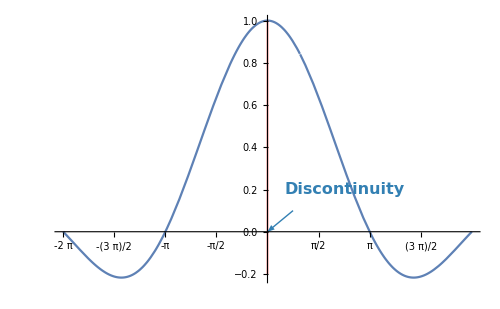

```mathematica
Show[pw1,myLine,myArrow,myText]
```

Example

Find the graph of the functions  {1-x^2, x<0
x+2, x ⩾ 0

```mathematica
Clear[f,x]
```

Let us plot and see ,

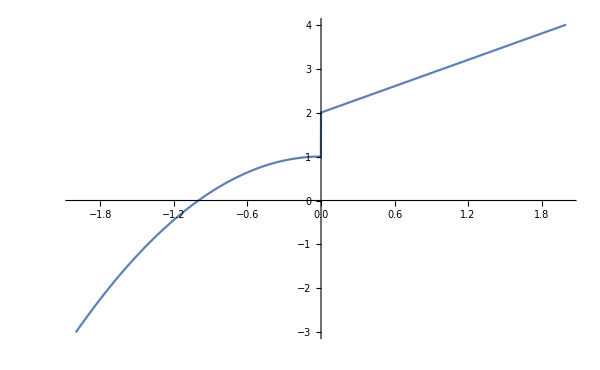

```mathematica
Plot[Piecewise[{{1-x^2, x<0},{x+2, x ⩾ 0}}],{x,-2,2}, Exclusions->None , ImageSize->600]
```

This two functions are not a true piecewise function. These are two different functions. Their structure and domains make them to seem as piecewise.

```mathematica
{Limit[1-x^2 , x -> 0-0] , Limit[x+2 , x -> 0+0]}
```

{1,2}

#### Example

Find the discontinuity of the function arctan(1/x )

Solution

```mathematica
Clear[f,x]
```

```mathematica
f[x_]:= ArcTan[1/x]
```

Let us plot this function :

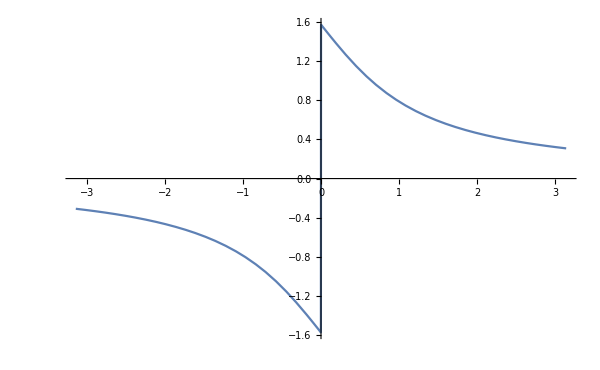

```mathematica
Plot[ArcTan[1/x],{x,-Pi,Pi},Exclusions->None , ImageSize->600]
```

The function has a discontinuity of the second kind (non-removable jump discontiniuty) at x =0. At least one of the side limits should be indeterminate (complex infinity).

```mathematica
{Limit[ArcTan[1/x], x-> 0-0],Limit[ArcTan[1/x], x-> 0+0]}
```

{Indeterminate,Indeterminate}

That show that the given function has a second class nonremovable essential discontinuty. The graph of the function in this case is extremely important. The values of the function at the near vicinity of the asymptotic line tending to the different infinities is only observable from the plot of these functions. Also careful attempts to assess the values in the vicinities of the asymptotic line is also informative.

```mathematica
{ArcTan[1/(0-0.00001)]  , ArcTan[1/(0+0.00001)]}
```

{-1.57079,1.57079}

This show that the observed function is a piecewise function. Let us plot it as a piecewise function.

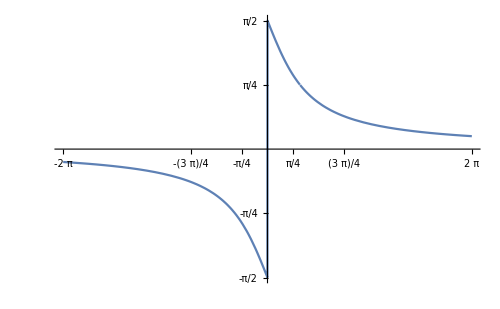

```mathematica
Plot[Piecewise[{{f[x],x<1},{f[x], x>1}}],{x, -2π,2π},Exclusions->{1},
PlotRange->{-π/2,π/2},
 Ticks-> {{-2π, -3/4  π,-1/4  π, 1/4  π,3/4  π,2π},{-1/2 π, -1/4  π,π,1/4  π,1/2π}},ImageSize->500]
```

#### Example

Find the points of discontinuity of the function f(x) =(|2x + 5|)/(2x + 5)

The point of discontinuity :

```mathematica
Clear[f,x]
f[x_]:= Abs[2x+5]/(2 x +5)
```

```mathematica
Solve[2x+5 == 0, x]
```

{{x→-5/2}}

This function is discontinous only at x = 5/2 and continious elsewhere. Let us plot and see its behavior :

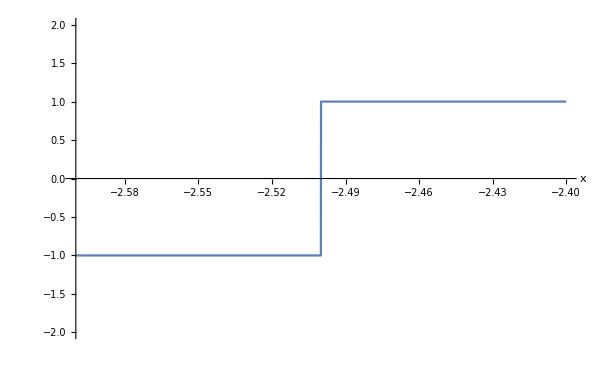

```mathematica
Plot[f[x], {x,-5/2 -0.1,-5/2+ 0.1},
PlotRange-> {-2,2},
Exclusions->None,
Axes->True,
AxesLabel-> Automatic,
ImageSize->600
]
```

The upper and lower limits :

```mathematica
{Limit[f[x], x-> -2.5-0],Limit[f[x], x-> -2.5+0]}
```

{Indeterminate,Indeterminate}

{Indeterminate, Indeterminate}

```mathematica
{f[-2.5-.001],f[-2.5 + 0.001]}
```

{-1.,1.}

Limits at the near neighborhood of the asymptotic line at x = -2.5 is found as indeterminate. But the values of the function in sufficient distance from the asymptotic line are real but not the same. Observations from the plot of these functions is of higher importance. The graph and algebraic results reveal that this function has a discontinuity of the first kind (removable discontinuity) at the point {-2.5,0}. The first kind discontinuity is of class B (removable jump discontinuity), since the values sufficiently away from the asymptotic line are real but different from each other. This a piecewise function whose enlarged graph is shown below.

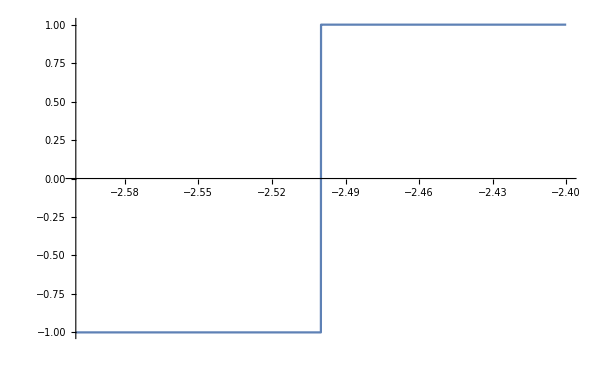

```mathematica
Plot[
Piecewise[{{f[x],x<2.5},{f[x],x>2.5}}],
{x,-2.6,-2.4},
Exclusions-> None,
ImageSize->600
]
```

Mathematica can handle more fine tunings on piecewise functions. More information may be found in Mathematica Definitions.

### Functions Plotted Together

Plotting functions together makes only sense if these functions share common domain of the common independent variable and give about the comparable values in the range of the dependent variable. Best examples may be sinus and cosinus functions.

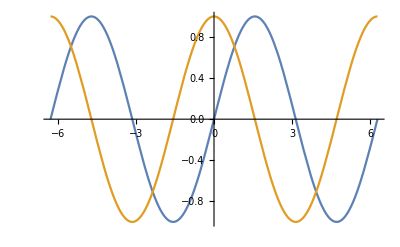

```mathematica
Plot[{Sin[x],Cos[x]},{x,-2π,2π}]
```

Adding Tooltip,

```mathematica
p1 =Plot[Tooltip[{Sin[x],Cos[x]}],
{x,-2π,2π}
]
```

-Graphics-

Adding PlotRegion and PlotRange,

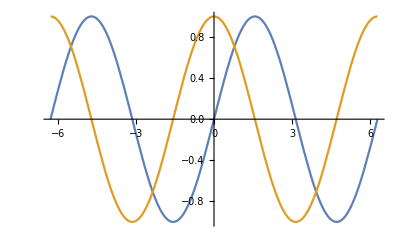

```mathematica
p1 =Plot[Tooltip[{Sin[x],Cos[x]}],
{x,-2π,2π},
PlotRegion->{-2Pi,2Pi},
PlotRange-> {-1,1}
]
```

About Dashing,

Dashing is a very advanced plot option for every distinguished plotted curves.
Dashing may be { Absolute (not dependent to image size) 
 Relative (dependent to image size)

Dashing is evaluated as succession of {trace,leaveBlank} successions. If they are equally spaced, giving only one measure will suffice as Dashing[Tiny].

Dashing may be given as  { Absolute Measures (Tiny,Medium,Large)                   
 Relative Numbers (fractions of the image size)

Dashing[{}] means, no dash, just a solid curve as evaluated by default, therefore there is no need to state.

Adding PlotStyle,

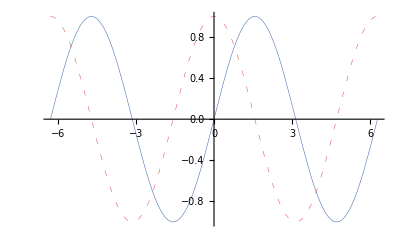

```mathematica
p1 =Plot[Tooltip[{Sin[x],Cos[x]}],
{x,-2π,2π},
PlotRegion->{-2Pi,2Pi},
PlotRange-> {-1,1},
PlotStyle->{
{Thickness[0.0008],Dashing[{}],RGBColor[0.12,0.32,0.62]},{Thickness[0.001],Dashing[{0.01,0.02}],RGBColor[0.89,0.34,0.36]}
}
]
```

Adding PlotLegends (added by default after the plot) ( they are also labeled by tooltips). Plot legends may be placed at “Before”,”Above”,”Below” and “After” as ex. PlotLegends → Placed[{“sin(x)”,”cos(x)”,After]. If “After is the choice, it is the default value and stating PlotLegends→ Expressions” will suffice.

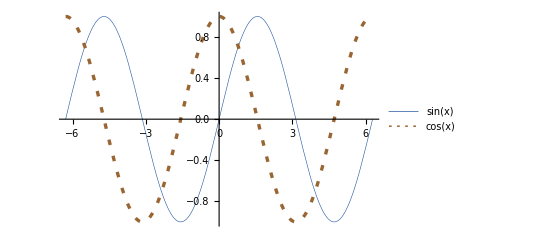

```mathematica
p1 =Plot[Tooltip[{Sin[x],Cos[x]}],
{x,-2π,2π},
PlotRegion->{-2Pi,2Pi},
PlotRange-> {-1,1},
PlotStyle->{
{Thickness[0.001],Dashing[{}],RGBColor[0.12,0.32,0.62]},{Thickness[0.006],Dashing[{0.01,0.02}],Brown}
},
PlotLegends->"Expressions"
]
```

Adding PlotLegends (Already visible by tooltips)

```mathematica
p1 =Plot[Tooltip[{Sin[x],Cos[x]}],
{x,-2π,2π},
PlotRegion->{-2Pi,2Pi},
PlotRange-> {-1,1},
PlotStyle->{
{Thickness[0.001],Dashing[{}],RGBColor[0.12,0.32,0.62]},{Thickness[0.006],Dashing[{0.01,0.02}],Brown}
},
(*PlotLegends->{{Style["sin(x)",RGBColor[0.12,0.32,0.62]]},{Style["cos(x)",Brown]}} *)
PlotLegends->{"sin(x)","cos(x)"}
]
```

-Graphics-

Those were for individual plots, now we can state the option for the whole plot. For avoiding the whole program to be cluttered, we have chosen to add them separateley using Show[ ] function. Since now we have all the data about the  individual plots as p1., we can now call Show [ ] function to display what we have in hand for the individual plots and add the new options about the whole plot.

```mathematica
Show[p1]
```

-Graphics-

It is showing all the up to date options for the individual curves. These can not be reached from Show[ ].
Adding the image size for the whole curve.

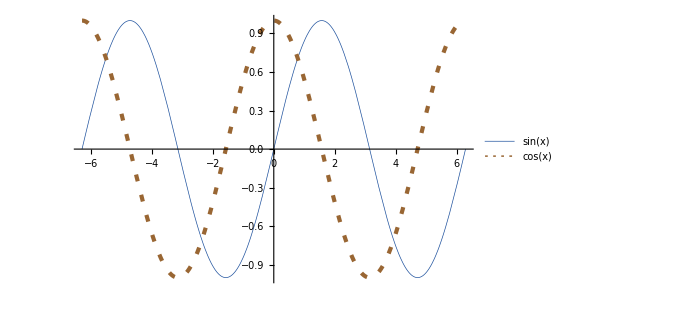

```mathematica
Show[p1 , ImageSize -> 500]
```

Adding background color (if it is wished as white, this the default color and no need to be given).

```mathematica
Show[p1, ImageSize-> 500,
Background -> White
]
```

-Graphics-

Adding axes. Axes may turn on by True, and off by False. If both will be True, there is no need to be stated since it is the default value.

```mathematica
Show[p1, ImageSize-> 500,
Background -> White,
Axes-> {True,True}
]
```

-Graphics-

Adding AxesOrigin. Default is {0,0} if it is the choice there is no need to state explicitly.

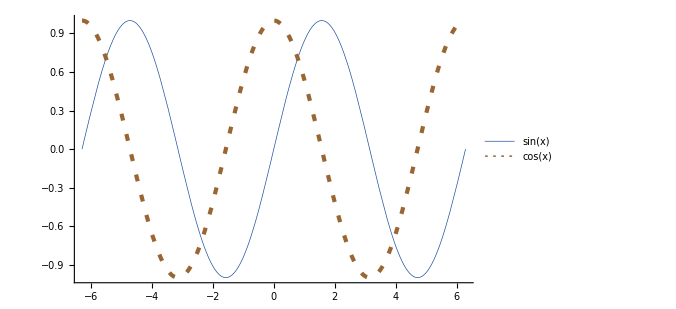

```mathematica
Show[p1, ImageSize-> 500,
Background -> White,
Axes-> {True,True},
AxesOrigin-> {0.0}
]
```

Adding PlotLabel,

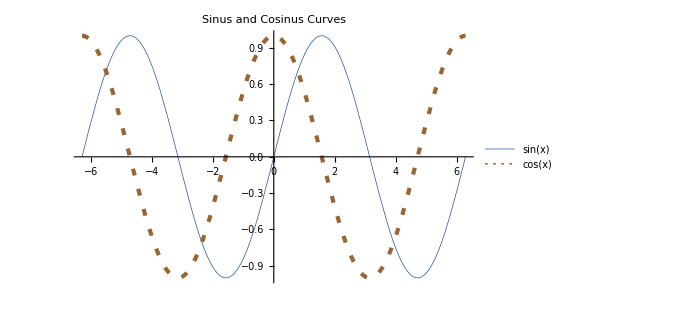

```mathematica
Show[p1, ImageSize-> 500,

PlotLabel-> Style["Sinus and Cosinus Curves\n",Red,FontFamily->"Segoe UI",FontSize->16]
]
```

We will peserve all the options for giving a chance to alter them for a new user. Decorating the axes,

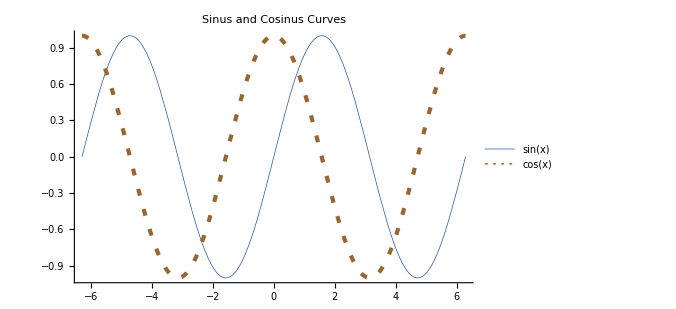

```mathematica
Show[p1, ImageSize-> 500,
Background -> White,
Axes-> {True,True},
AxesOrigin-> {0.0},
PlotLabel-> Style["Sinus and Cosinus Curves\n",Red,FontFamily->"Segoe UI",FontSize->16],
AxesStyle -> {Directive[Red,12],Directive[Blue,12]}
]
```

Labeling axes,

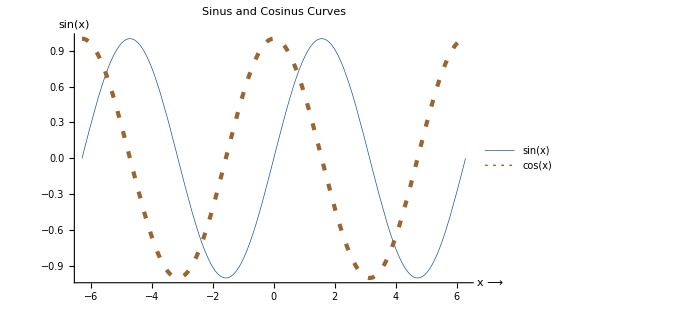

```mathematica
Show[p1, ImageSize-> 500,
Background -> White,
Axes-> {True,True},
AxesOrigin-> {0.0},
PlotLabel-> Style["Sinus and Cosinus Curves\n",Red,FontFamily->"Segoe UI",FontSize->16],
AxesStyle -> {Directive[Red,12],Directive[Blue,12]},
AxesLabel-> {"\nx  ⟶","\nsin(x)"} 
]
```

Well, the general impression is not favorable for the axes labeled at the end of the axes, so we will present another possibilities, either to frame all or place them with programming steps but if this plot is the final design the using ``Drawing Tools” is much faster for any one who is not willing to jump out to the deeper functions of the Mathematica. Any way we will continue by programming.

Axes Ticks,

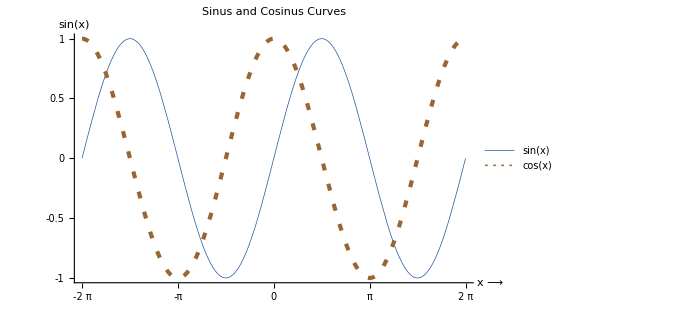

```mathematica
Show[p1, ImageSize-> 500,
Background -> White,
Axes-> {True,True},
AxesOrigin-> {0.0},
PlotLabel-> Style["Sinus and Cosinus Curves\n",Red,FontFamily->"Segoe UI",FontSize->16],
AxesStyle -> {Directive[Red,20],Directive[Blue,16]},
AxesLabel-> {"\n\ x ⟶","\nsin(x)"},
Ticks-> {{-2π, -(3 π)/2,-π,-π/2,0,π/2,π,(3 π)/2,2π},{-1,-0.75,-0.5,-0.25,0,0.25,0.50,0.75,1}}
]
```

Grid Lines

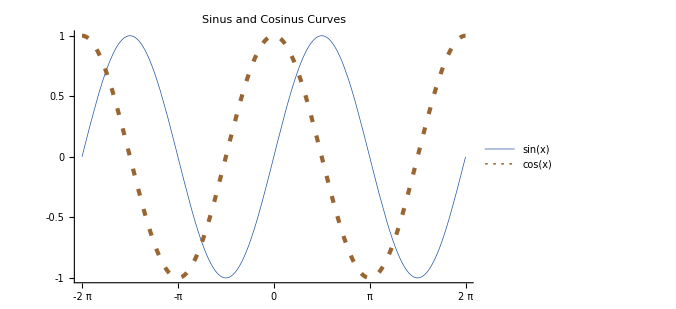

```mathematica
Show[p1, ImageSize-> 500,
Background -> White,
Axes-> {True,True},
AxesOrigin-> {0.0},
PlotLabel-> Style["Sinus and Cosinus Curves\n",Red,FontFamily->"Segoe UI",FontSize->20],
AxesStyle -> {Directive[Red,20],Directive[Blue,16]},

Ticks-> {{-2π, -(3 π)/2,-π,-π/2,0,π/2,π,(3 π)/2,2π},{-1,-0.75,-0.5,-0.25,0,0.25,0.50,0.75,1}},
GridLines-> {{-2π, -(7 π)/4,-(3 π)/2,-(5 π)/4,-π, -(3 π)/4,-π/2,-π/4,0,π/4,π/2,(3π)/4,π,(5π)/4,(3 π)/2,(7π)/4,2π},{-1,-0.75,-0.5,-0.25,0,0.25,0.50,0.75,1}}
]
```

Configuring the grid lines,

```mathematica
Show[p1, ImageSize-> 500,
Background -> White,
Axes-> {True,True},
AxesOrigin-> {0.0},
PlotLabel-> Style["Sinus and Cosinus Curves\n",Red,FontFamily->"Segoe UI",FontSize->20],
AxesStyle -> {Directive[Red,20],Directive[Blue,16]},

Ticks-> {{-2π, -(3 π)/2,-π,-π/2,0,π/2,π,(3 π)/2,2π},{-1,-0.75,-0.5,-0.25,0,0.25,0.50,0.75,1}},
GridLines-> {{-2π, -(7 π)/4,-(3 π)/2,-(5 π)/4,-π, -(3 π)/4,-π/2,-π/4,0,π/4,π/2,(3π)/4,π,(5π)/4,(3 π)/2,(7π)/4,2π},{-1,-0.75,-0.5,-0.25,0,0.25,0.50,0.75,1}},

GridLinesStyle->{{Directive[Orange,Dashed]},{Directive[Blue,Dashed]}}
]
```

-Graphics-

Framing the whole plot,

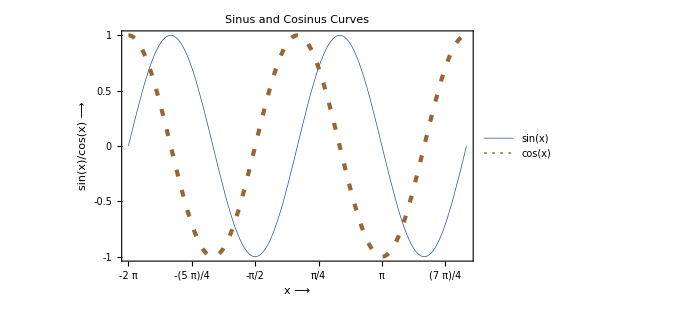

```mathematica
Show[p1, ImageSize-> 500,
Frame->{{True,False},{True,False}},
FrameLabel->{Style["x ⟶",Red,FontFamily->"SegoeUI",FontSize->  20],Style["sin(x)/cos(x) ⟶",Blue,FontFamily->"SegoeUI",FontSize->  20]},
FrameStyle-> {Blue,Red},
Background -> White,
Axes-> {True,True},
AxesOrigin-> {0.0},
PlotLabel-> Style["Sinus and Cosinus Curves\n",Red,FontFamily->"Segoe UI",FontSize->20],
AxesStyle -> {Directive[Red,20],Directive[Blue,20]},

FrameTicks-> {{-2π, -(7 π)/4,-(3 π)/2,-(5 π)/4,-π, -(3 π)/4,-π/2,-π/4,0,π/4,π/2,(3π)/4,π,(5π)/4,(3 π)/2,(7π)/4,2π},{-1,-0.75,-0.5,-0.25,0,0.25,0.50,0.75,1}},
GridLines-> {{-2π, -(7 π)/4,-(3 π)/2,-(5 π)/4,-π, -(3 π)/4,-π/2,-π/4,0,π/4,π/2,(3π)/4,π,(5π)/4,(3 π)/2,(7π)/4,2π},{-1,-0.75,-0.5,-0.25,0,0.25,0.50,0.75,1}},

GridLinesStyle->{{Directive[Lighter[Red],Dashed]},{Directive[Lighter[Blue],Dashed]}}
]
```

Altering the image size,

```mathematica
Show[p1, ImageSize-> 500,
Frame->{{True,False},{True,False}},
FrameLabel->{Style["x ⟶",Red,FontFamily->"SegoeUI",FontSize->  20],Style["sin(x)/cos(x) ⟶",Blue,FontFamily->"SegoeUI",FontSize->  20]},
FrameStyle-> {Blue,Red},
Background -> White,
Axes-> {True,True},
AxesOrigin-> {0.0},
PlotLabel-> Style["Sinus and Cosinus Curves\n",Red,FontFamily->"Segoe UI",FontSize->20],
AxesStyle -> {Directive[Red,20],Directive[Blue,20]},

FrameTicks-> {{-2π, -(7 π)/4,-(3 π)/2,-(5 π)/4,-π, -(3 π)/4,-π/2,-π/4,0,π/4,π/2,(3π)/4,π,(5π)/4,(3 π)/2,(7π)/4,2π},{-1,-0.75,-0.5,-0.25,0,0.25,0.50,0.75,1}},
GridLines-> {{-2π, -(7 π)/4,-(3 π)/2,-(5 π)/4,-π, -(3 π)/4,-π/2,-π/4,0,π/4,π/2,(3π)/4,π,(5π)/4,(3 π)/2,(7π)/4,2π},{-1,-0.75,-0.5,-0.25,0,0.25,0.50,0.75,1}},

GridLinesStyle->{{Directive[Lighter[Red],Dashed]},{Directive[Lighter[Blue],Dashed]}}
]
```

-Graphics-

Last possibility is to work direcly with the plot, by using graphic primitives and without frames,

```mathematica
text1= Graphics[Text[Style["x ⟶",FontSize-> 18,Red,FontWeight->"Normal"], {3.5,-0.3},{0,0},{1,0}]];
```

```mathematica
text2= Graphics[Text[Style["sin(x) or cos (x) ⟶",FontSize-> 18,FontWeight->"Normal",RGBColor[0,0.2,0.7]], {-π/4,0},{0,0},{0,1}]];
```

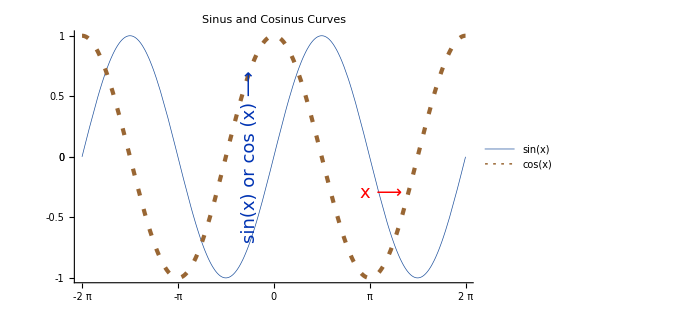

```mathematica
Show[p1,text1,text2,
 ImageSize-> 500,
Background -> White,
Axes-> {True,True},
AxesOrigin-> {0.0},
PlotLabel-> Style["Sinus and Cosinus Curves\n",Red,FontFamily->"Segoe UI",FontSize->16],
AxesStyle -> {Directive[Red,20],Directive[Blue,16]},
Ticks-> {
{-2π, -(3 π)/2,-π,-π/2,0,π/2,π,(3 π)/2,2π},
{-1,-0.5,0,0,0.50,1}
},
GridLines-> {
{-2π, -(7 π)/4,-(3 π)/2,-(5 π)/4,-π, -(3 π)/4,-π/2,-π/4,0,π/4,π/2,(3π)/4,π,(5π)/4,(3 π)/2,(7π)/4,2π},{-1,-0.75,-0.5,-0.25,0,0.25,0.50,0.75,1}
},

GridLinesStyle->{{Directive[Red,Dashed]},{Directive[Blue,Dashed]}}
]
```

Usage of these plot templates

Problem :

Plot y = x^2 + x^5 where the domain of x will be [-10 , 10]. (University of Texas in Austin)

Solution :

It is strongly advisable to make a very basic plot of any function to be plotted, ther we can see what will its behavior and assess the domain and range intervals for a detailed plot.

```mathematica
Clear[f,x]
```

```mathematica
f[x_]:=  x^2+x^5
```

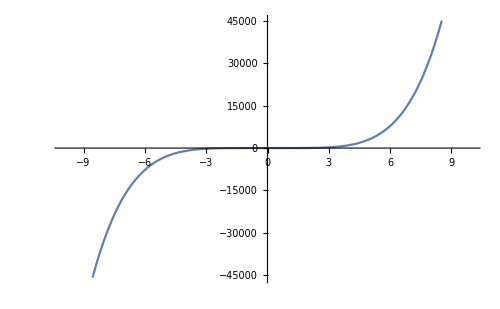

```mathematica
Plot[f[x],{x, -10,10},ImageSize-> 500]
```

Well, it seems the is a second kind discontinuity at x=-10 and x=10. Let us see the limits :

```mathematica
Limit[f[x], x->-10-0] (* Left Side (Lower) Limit *)
```

-99900

```mathematica
Limit[f[x], x->-10+0] (* Right Side (Upper) Limit *)
```

-99900

We will also contol the value of the function in these pseudo asymptotic lines,

```mathematica
f[-∞]
```

Infinity::indet: Indeterminate expression -∞+∞ encountered.

Indeterminate

The results show that the function has no real asymptotes at the points x=-10 and x=10 . But there is no point to examine his domain beyond x=-10 and x=10 since the range evaluates to the extremely high values which are not representable by 2D x/y plots.

It is better to examine this function in the region [-5,5] :

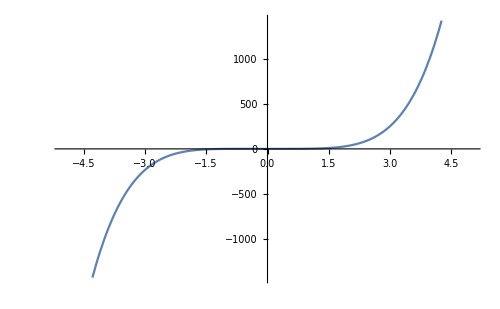

```mathematica
Plot[f[x],{x, -5,5},ImageSize-> 500]
```

The function seems to have a root and inflexion point at x = 0. Let’s chek it :

```mathematica
f[0]
```

0

Right, it has actually a root at x = 0. For the evaluation of the inflexion point we’ll leave for the detailed mathematical analysis. We will only try to plot this function.

Let us import one of the templates developed at this page and presented above and change the values according to our first observations of the given function.

```mathematica
Clear[text1,text2,p1]
```

```mathematica
p1 =Plot[Tooltip[{x^2 +   x^5}],
{x,-10,10},
PlotRegion-> All,
PlotRange-> Automatic,
PlotStyle->{
Thickness[0.001],Dashing[{}],RGBColor[0.12,0.32,0.62]
},
PlotLegends->Automatic
];
```

```mathematica
text1= Graphics[Text[Style["x ⟶",FontSize-> 16,Red,FontWeight->"Normal"], {5,-10000},{0,0},{1,0}]];
```

```mathematica
text2= Graphics[Text[Style["y ⟶",FontSize-> 16,FontWeight->"Normal",RGBColor[0,0.2,0.7]], {-3,20000},{0,0},{0,1}]];
```

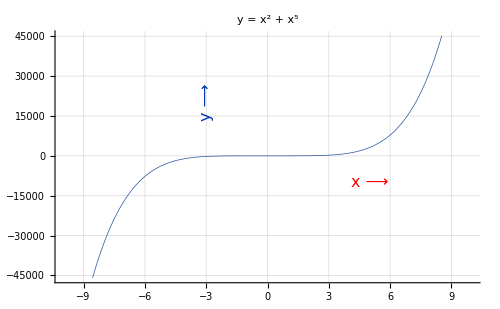

```mathematica
Show[p1,text1,text2,
 ImageSize-> 500,
Background -> White,
Axes-> {True,True},
AxesOrigin-> {0.0},
PlotLabel-> Style["y = x^2 + x^5\n",Red,FontFamily->"Segoe UI",FontSize->22],
AxesStyle -> {Directive[Red,16],Directive[Blue,16]},
Ticks-> Automatic,
GridLines->Automatic,
GridLinesStyle->{{Directive[Red,Dashed]},{Directive[Blue,Dashed]}}
]
```

It has taken considerably less time for getting a presentable plot.

Problem :

Plot y = 1 +Sin[2 π x]/(x^2+1) and inspect.

Solution :

```mathematica
Clear[f,x,p1,text1,text2]
```

```mathematica
f[x_]:= 1 +Sin[2 π x]/(x^2+1)
```

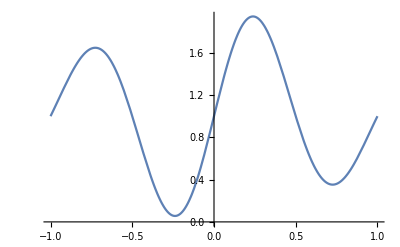

```mathematica
Plot[f[x],{x,Automatic,Automatic}]
```

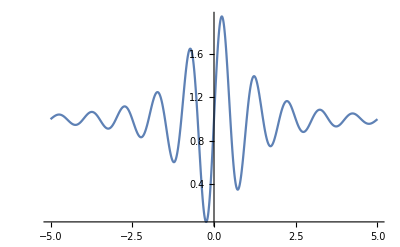

```mathematica
Plot[f[x],{x,-5,5}, PlotRange->All]
```

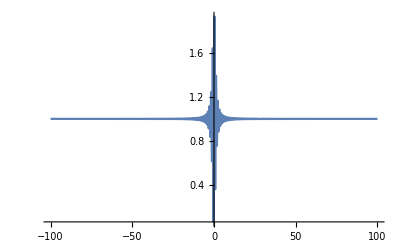

```mathematica
Plot[f[x],{x,-100,100}, PlotRange->All]
```

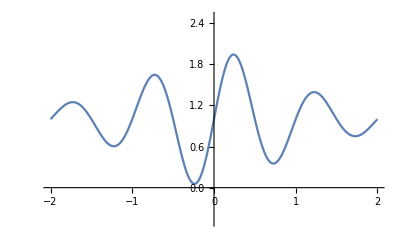

```mathematica
Plot[f[x],{x,-2,2}, PlotRange->{-0.5,2.5}]
```

```mathematica
p1 =Plot[Tooltip[{1 +Sin[2 π x]/(x^2+1)}],
{x,-2.02,2.02},
PlotRegion-> All,
PlotRange-> {-1.02,2.502},
PlotStyle->{
Thickness[0.001],Dashing[{}],RGBColor[0.12,0.32,0.62]
},
PlotLegends->Automatic
];
```

```mathematica
text1= Graphics[Text[Style["x ⟶",FontSize-> 16,Red,FontWeight->"Normal"], {1,-0.4},{0,0},{1,0}]];
```

```mathematica
text2= Graphics[Text[Style["y ⟶",FontSize-> 16,FontWeight->"Normal",RGBColor[0,0.2,0.7]], {-.25,1.0},{0,0},{0,1}]];
```

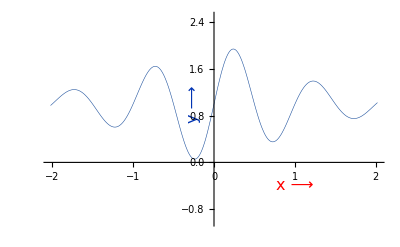

```mathematica
Show[p1,text1,text2
]
```

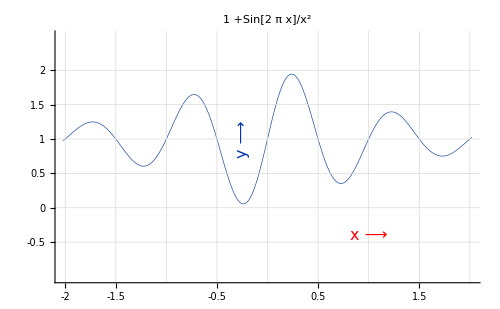

```mathematica
Show[p1,text1,text2,
 ImageSize-> 500,
Background -> White,
Axes-> {True,True},
AxesOrigin-> {0.0},
PlotLabel-> Style["1 +Sin[2 π x]/x^2\n",Red,FontFamily->"Segoe UI",FontSize->16],
AxesStyle -> {Directive[Red,16],Directive[Blue,16]},
Ticks-> {
{-2, -1.75,-1.5,-1,-0.5,0,0.5,1,1.5,2},
{-.5,0,0.5,1,1.5,2}
},
GridLines-> {
{-2, -1.5,-1,-0.5,0,0.5,1,1.5,2},
{-.5,0,0.5,1,1.5,2}
},

GridLinesStyle->{{Directive[Red,Dashed]},{Directive[Blue,Dashed]}}
]
```

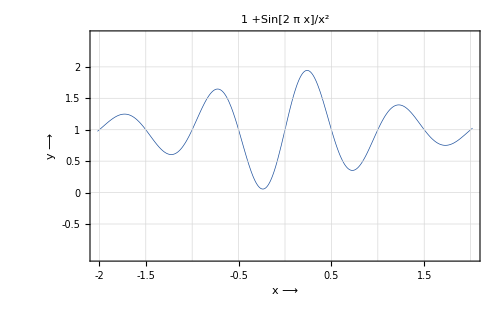

```mathematica
Show[p1, ImageSize-> 500,
Frame-> {{True,True},{True, True}},
FrameLabel->{{Style["y ⟶",Blue,FontFamily->"SegoeUI",FontSize->  18],None},
{Style["x ⟶",Red,FontFamily->"SegoeUI",FontSize->  18],None}},
FrameStyle-> {Blue,Red},
Background -> White,
Axes-> {True,True},
AxesOrigin-> {0.0},
PlotLabel-> Style["1 +Sin[2 π x]/x^2\n",Red,FontFamily->"Segoe UI",FontSize->16],
AxesStyle -> {Directive[Red,16],Directive[Blue,16]},
FrameTicks-> {{{-.5,0,0.5,1,1.5,2},None},
{{-2, -1.75,-1.5,-1,-0.5,0,0.5,1,1.5,2},None}},

GridLines-> {
{-2, -1.5,-1,-0.5,0,0.5,1,1.5,2},
{-.5,0,0.5,1,1.5,2}
},

FrameTicksStyle->{{{Thick,Directive[FontSize->16]},None},{{Thick,Directive[FontSize->16]},None}},

GridLinesStyle->{{Directive[Red,Dashed]},{Directive[Blue,Dashed]}}
]
```

```mathematica
Plot[Tooltip[{1 +Sin[2 π x]/(x^2+1)}],
{x,-2.02,2.02},
PlotRegion-> All,
PlotRange-> {-1.02,2.502},
PlotStyle->{
Thickness[0.001],Dashing[{}],RGBColor[0.12,0.32,0.62]
},
PlotLegends->Automatic,
 ImageSize-> 500,
Frame-> {{True,True},{True, True}},
FrameLabel->{{Style["y ⟶",Blue,FontFamily->"SegoeUI",FontSize->  18],None},
{Style["x ⟶",Red,FontFamily->"SegoeUI",FontSize->  18],None}},
FrameStyle-> {Blue,Red},
Background -> White,
Axes-> {True,True},
AxesOrigin-> {0.0},
PlotLabel-> Style["1 +Sin[2 π x]/x^2\n",Red,FontFamily->"Segoe UI",FontSize->16],
AxesStyle -> {Directive[Red,16],Directive[Blue,16]},
FrameTicks-> {{{-.5,0,0.5,1,1.5,2},None},
{{-2, -1.75,-1.5,-1,-0.5,0,0.5,1,1.5,2},None}},

GridLines-> {
{-2, -1.5,-1,-0.5,0,0.5,1,1.5,2},
{-.5,0,0.5,1,1.5,2}
},

FrameTicksStyle->{{{Thick,Directive[FontSize->16]},None},{{Thick,Directive[FontSize->16]},None}},

GridLinesStyle->{{Directive[Red,Dashed]},{Directive[Blue,Dashed]}}
]
```

-Graphics-

Just change the inputs with yours...

Last assays are near publication quality.

Mathematica has many other options to enhancing the plots. Here, we have only presented some of them, useful for having fully decorated plots.
Happy ploting...